### This is a different blue from the other list plots

```mathematica
progress =Module[{sorted = SortBy[Select[Values[{{"[◼]", "Data"}}["$LifeData"]],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData["DefaultPlotColors"][1]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
progress2 =DeleteCases[Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData["DefaultPlotColors"][1]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress2, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress2[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 100}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0,3}}]
```

-Graphics-

### Clean up 3

Some are “tightly integrated”, while some have many “modular pieces”, as revealed by their causal graphs:

Clean up

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[BoundingBoxLayeredGraph[#,#Period,ImageSize->{Automatic,140}],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{{2,3,4,5,6,7,8,9,10},{12,15,16,20,21,30,36}},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-period 10  -Graphics-period 12  
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-period 20  
-Graphics-period 21  
-Graphics-
-Graphics-period 30  
-Graphics-period 36

```mathematica
byp=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&MemberQ[{2,3,4,5,6,7,8,9,10,12,15,16,20,21,30,36}, #["Period"]] &]],#Period&]),#[[1,"Period"]]&];
```

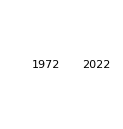
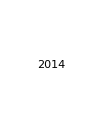
-Graphics--Graphics-period 2-Graphics-period 3-Graphics-period 4-Graphics-period 5-Graphics-period 6-Graphics-period 7-Graphics-period 8-Graphics-period 9-Graphics-period 10-Graphics-period 12-Graphics-period 15-Graphics-period 16-Graphics-period 20-Graphics-period 21-Graphics-period 30-Graphics-period 36

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[BoundingBoxLayeredGraph[#, Automatic, ImageSize-> {If[#Period == 30, 50, Automatic], 100}],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@# (*ImageSize->{{20,300},{10,100}}*)],Style[Text["period "<>ToString@#[[1]]["Period"]], 10],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[byp],Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.8]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]],LineSpacing->{1,1}]
```

### Try to get “trails” ... and a few nearby gliders, etc...

One might expect this repeated behavior to continue forever.  But in a typical manifestation of computational irreducibility, it doesn’t, instead stopping its “regeneration” after 24 cycles, and then reaching a steady state (apart from “radiated” gliders) after 3911 steps:

Try to get “trails” ... and a few nearby gliders

```mathematica
CellularAutomatonSpacetimePlot["GameOfLife",#,1000,Mesh->None,"Decay"->.99]&/@CellularAutomaton["GameOfLife",{Normal[SparseArray[…]],0},{{0,4000,1000}}]
```

Make 4 panels on the right, letting the gliders go out of frame

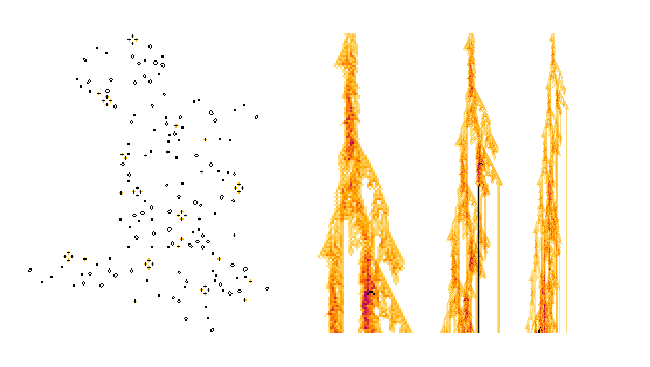

```mathematica
GraphicsRow[Join[{CellularAutomatonHistoryPlot["GameOfLife",SparseArray[…],20,Mesh->False]},{{"[◼]", "CellularAutomatonSpacetimePlot2"}}["GameOfLife",{SparseArray[…],0},#,
"Decay"->.99,Mesh->(#<101),ColorRules->{-1->Black, x_/; x!=-1:>Blend[{{0,RGBColor[1., 1., 1.]},{.01,RGBColor[1., 0.9461, 0.7000000000000001]},{.3,RGBColor[1., 0.66, 0.]},{.5,RGBColor[0.98, 0.42, 0.04]},{.8,RGBColor[0.7000000000000001, 0., 0.37800000000000006]}},x]}]&/@{150,300, 600, 1000}]]
```

### Show multiple panels of slices, etc...

produces a structure that keeps generating a “periodic wake” forever:

Show multiple panels of slices
Maybe only use 3D if that’s what’s done in the previous example

Rotate these to the correct direction

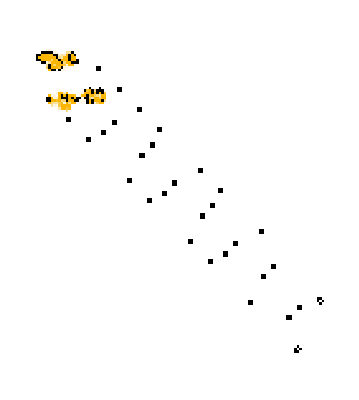
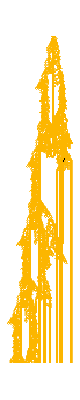
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200]}
```

```mathematica
GraphicsRow[Join[{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False], CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200, ImageSize->{Automatic, 440}, ViewPoint->{1.3,2.4,1.8}]},{{"[◼]", "CellularAutomatonSpacetimePlot2"}}["GameOfLife",{Transpose@SparseArray[…],0},#,
"Decay"->.99,Mesh->False,ColorRules->{-1->Black, x_/; x!=-1:>Blend[{{0,RGBColor[1., 1., 1.]},{.01,RGBColor[1., 0.9461, 0.7000000000000001]},{.3,RGBColor[1., 0.66, 0.]},{.5,RGBColor[0.98, 0.42, 0.04]},{.8,RGBColor[0.7000000000000001, 0., 0.37800000000000006]}},x]}]&/@{100, 200, 300, 400}]]
```

-Graphics-

### Clean up; fix sizing, etc...

What about the causal graphs?  Basically these just decrease in “width” (i.e. number of independent modular parts) as the number of engines decreases:

Clean up; fix sizing etc.
Possibly go to two rows

```mathematica
GraphicsRow[ParallelMap[Labeled[Framed[First@WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[$LifeData[#],96]],FrameStyle->Opacity[.3]],Text[Style[Column[{$LifeData[#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic]},Center],10]]]&,{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"}],Spacings->5]
```

The uncompressed graphic is saved in the directory Graphics-Draft-06 with filenames 2025022801205227295.png and 2025022801205227295.nb

-Graphics-

```mathematica
Row[ParallelMap[
Labeled[
Rasterize[Framed[First@WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[$LifeData[#],96, ImageSize->{Automatic, 200}]],FrameStyle->Opacity[.3]], ImageSize->{Automatic, 150}],Text[Style[Column[{$LifeData[#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic]},Center],10]]]&,{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"}],Spacer[1]]
```

-Graphics-1991
(13 engines)-Graphics-1991
(10 engines)-Graphics-1993
(7 engines)-Graphics-1998
(6 engines)-Graphics-1998
(8 engines)-Graphics-2004
(3 engines)-Graphics-2005
(4 engines)-Graphics-2005
(5 engines)-Graphics-2017
(2 engines)

### Add the recent period 80 one from above

Over the years, a whole variety of different glider guns have been found. Some are in effect “thoroughly controlled” constructions. Others are more based on some complex process that is reined in to the point where it just produces a stream of gliders and nothing more:

Add the recent period 80 one from above
Get rid of braces and commas

```mathematica
trueguns=Join[$LifeData/@{"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"},
{<|"MatrixData"->SparseArray[…],"Period"->15,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->16,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->20,"Year"->2021|>,
<|"MatrixData"->SparseArray[…],"Period"->21,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->35,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->37,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->40,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->47,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>}];
```

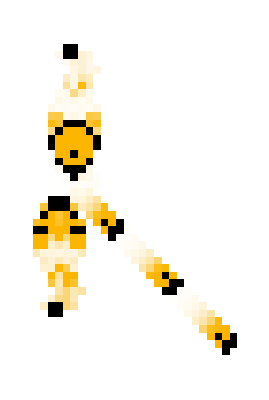
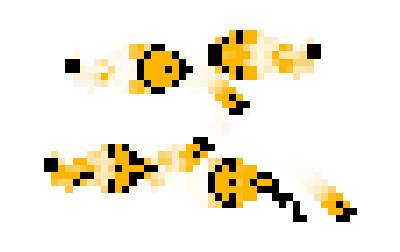
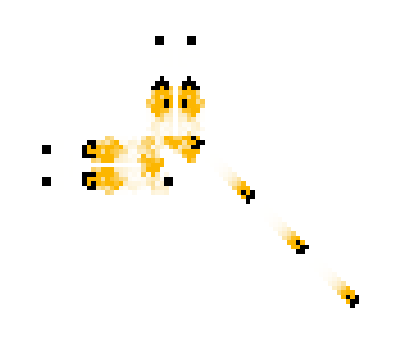
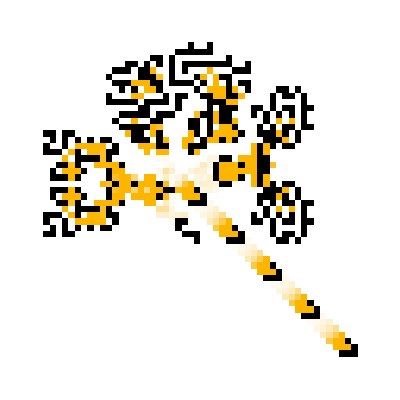
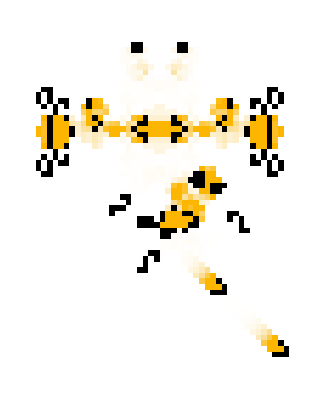
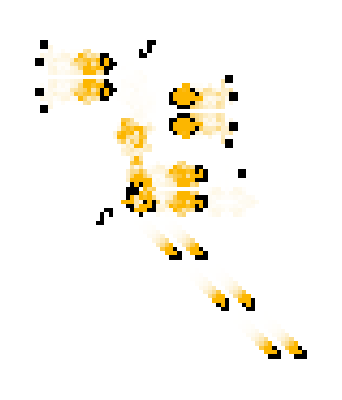
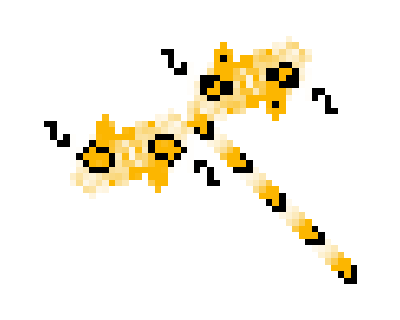
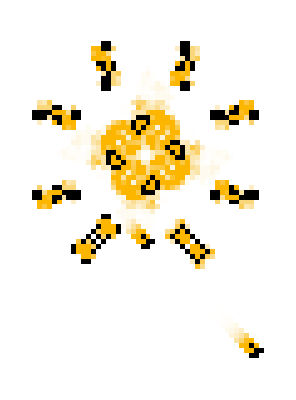
{-Graphics-1970
(period 30),-Graphics-1970
(period 60),-Graphics-1971
(period 46),-Graphics-1997
(period 24),-Graphics-1997
(period 44),-Graphics-1997
(period 46),-Graphics-2000
(period 22),-Graphics-2009
(period 88),-Graphics-2010
(period 45),-Graphics-2013
(period 94),-Graphics-2017
(period 92),-Graphics-2018
(period 33),-Graphics-2021
(period 20),-Graphics-2021
(period 54),-Graphics-2021
(period 55),-Graphics-2022
(period 40),-Graphics-2022
(period 21),-Graphics-2022
(period 37),-Graphics-2022
(period 32),-Graphics-2022
(period 28),-Graphics-2022
(period 25),-Graphics-2022
(period 27),-Graphics-2022
(period 34),-Graphics-2022
(period 43),-Graphics-2022
(period 48),-Graphics-2022
(period 51),-Graphics-2023
(period 41),-Graphics-2023
(period 49),-Graphics-2023
(period 61),-Graphics-2024
(period 16),-Graphics-2024
(period 15),-Graphics-2024
(period 36),-Graphics-2024
(period 53),-Graphics-2025
(period 47),-Graphics-2025
(period 35)}

```mathematica
Style[MapIndexed[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[#Period<60,3#Period,1#Period],Mesh->None,ImageSize->{Automatic,80}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&,SortBy[trueguns,#Year&]],LineSpacing->{1.1,1}]
```

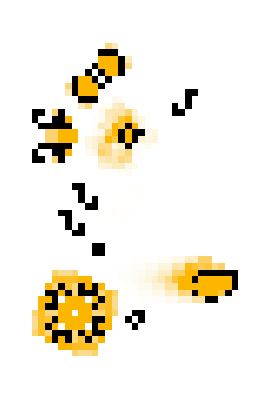
-Graphics-1970
(period 30)-Graphics-1970
(period 60)-Graphics-1971
(period 46)-Graphics-1997
(period 24)-Graphics-1997
(period 44)-Graphics-1997
(period 46)-Graphics-2000
(period 22)-Graphics-2009
(period 88)-Graphics-2010
(period 45)-Graphics-2013
(period 94)-Graphics-2017
(period 92)-Graphics-2018
(period 33)-Graphics-2021
(period 20)-Graphics-2021
(period 54)-Graphics-2021
(period 55)-Graphics-2022
(period 40)-Graphics-2022
(period 21)-Graphics-2022
(period 37)-Graphics-2022
(period 32)-Graphics-2022
(period 28)-Graphics-2022
(period 25)-Graphics-2022
(period 27)-Graphics-2022
(period 34)-Graphics-2022
(period 43)-Graphics-2022
(period 48)-Graphics-2022
(period 51)-Graphics-2023
(period 41)-Graphics-2023
(period 49)-Graphics-2023
(period 61)-Graphics-2024
(period 16)-Graphics-2024
(period 15)-Graphics-2024
(period 36)-Graphics-2024
(period 53)-Graphics-2025
(period 47)-Graphics-2025
(period 35)-Graphics-2025
(period 80)

```mathematica
Style[
Row[MapIndexed[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[#Period<60,3#Period,1#Period],Mesh->None,ImageSize->{Automatic,80}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&,SortBy[trueguns,#Year&]], Spacer[2]],LineSpacing->{1.1,1}]
```

### Fix the weird linewrap

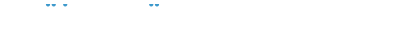
-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-period 21

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->If[#Name ==="Mold", 22.5, 3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

### Make intermediate dots gray

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[RGBColor[0.24, 0.6, 0.8], PointSize[.011]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted,HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}
]
```

-Graphics-

```mathematica
ListPlot[Function[pds,
MapIndexed[
Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, If[Last[#2] == Length[pds], RGBColor[0.24, 0.6, 0.8], None]]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&
, pds]]/@ (SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[Lighter[Gray], PointSize[.01]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted,HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}]
```

-Graphics-

This was a slightly lighter blue which I changed

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}];
```

```mathematica
redidxs =With[{ps = PositionSmallest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
blueidxs = With[{ps = PositionSmallest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,If[MatchQ[#,_Rational],InputForm[#], Row[{"√5","/",6}] ]}&/@DeleteCases[Union[Last/@data],1/8|1/7],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle->RGBColor[0.24, 0.6, 0.8],
PlotMarkers->Catenate[MapIndexed[{Rotate[Graphics[{{AbsolutePointSize[5],Style[Point[{0, 0}], If[Last[#2] == redidxs[First[#2]], Red, None]]},Style[Text[Style["⟶",Bold, GrayLevel[.2],7],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&, as, {2}]], PlotRangePadding->{{Automatic, .2}, {Automatic, 0}}, GridLines->{None, Automatic}, GridLinesStyle->Directive[Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted]]]
```

-Graphics-

Can’t remember if you wanted these guys gray as well:

```mathematica
blueidxs = With[{ps = PositionLargest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,If[MatchQ[#,_Rational],InputForm[#], Row[{"√5","/",6}] ]}&/@DeleteCases[Union[Last/@data],1/8|1/7],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle->Lighter[Gray],
PlotMarkers->Catenate[MapIndexed[{Rotate[Graphics[{{AbsolutePointSize[5],Style[Point[{0, 0}], If[Last[#2] == redidxs[First[#2]], Red, If[Last[#2] == blueidxs[First[#2]],RGBColor[0.24, 0.6, 0.8],  None]]]},Style[Text[Style["⟶",Bold, GrayLevel[.2],7],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&, as, {2}]], PlotRangePadding->{{Automatic, .2}, {Automatic, 0}}, GridLines->{None, Automatic}, GridLinesStyle->Directive[Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted]]]
```

-Graphics-

### Fix the opacities Put vertical gray lines in Fix the spacing of labels from array plots; possibly line up the labels

Some attempts, I think I can finnegle and epilogue if needed

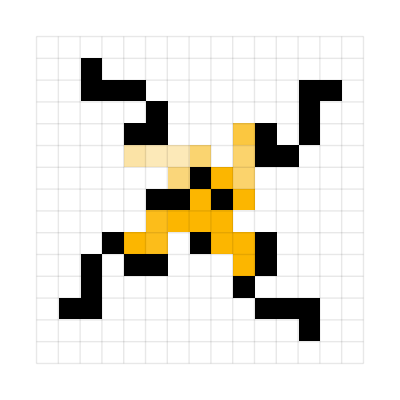
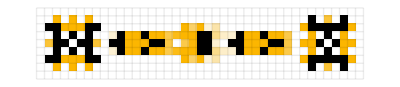
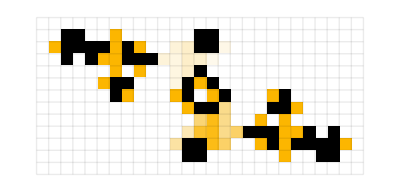
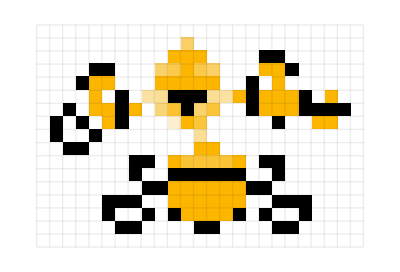
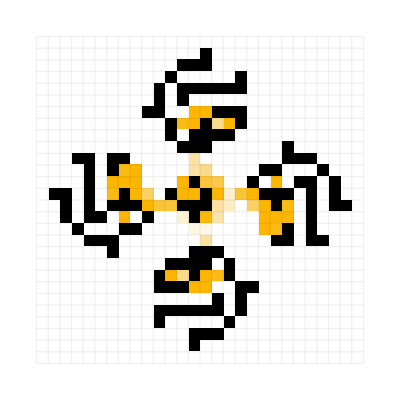
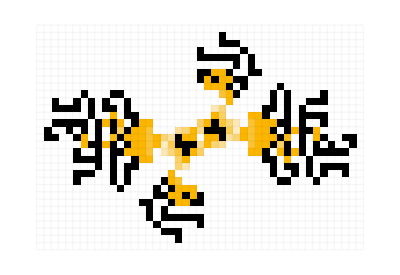
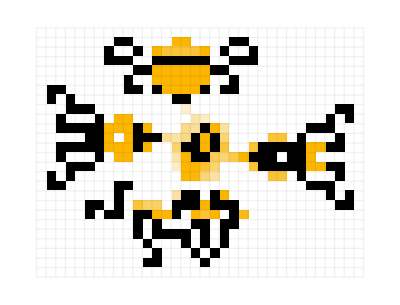
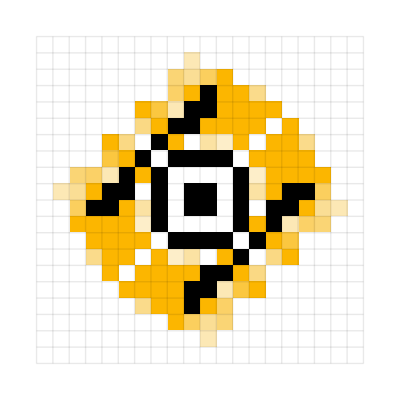
-Graphics-1972-Graphics-1984-Graphics-1989-Graphics-1994-Graphics-1995-Graphics-1995-Graphics-2004-Graphics-2009-Graphics-2015-Graphics-2019-Graphics-2021-Graphics-2022-Graphics-2022-Graphics-2023-Graphics-2023

```mathematica
Style[With[{data=Quiet[Append[Append[KeyDrop[Select[$LifeData,#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},Row[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[(.7/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->18Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,Gray]]]&/@SortBy[data,#["Year"]&]],Spacer[4]]],LineSpacing->{1,1}]
```

```mathematica
Style[With[{data=Quiet[Append[Append[KeyDrop[Select[$LifeData,#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},Grid[Partition[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[(.8/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->18Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,Gray]]]&/@SortBy[data,#["Year"]&]], 5], Alignment->Bottom, Spacings->0]],LineSpacing->{1,1}]
```

-Graphics-1972 | -Graphics-1984 | -Graphics-1989 | -Graphics-1994 | -Graphics-1995
-Graphics-1995 | -Graphics-2004 | -Graphics-2009 | -Graphics-2015 | -Graphics-2019
-Graphics-2021 | -Graphics-2022 | -Graphics-2022 | -Graphics-2023 | -Graphics-2023

```mathematica
Style[With[{data=Quiet[Append[Append[KeyDrop[Select[$LifeData,#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},
Grid[
Catenate[Transpose/@Partition[Values[{CellularAutomatonHistoryPlot["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[(.8/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->18Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,Gray]]}&/@SortBy[data,#["Year"]&]], 5]], Alignment->Center, Spacings->{{2->-.5, 0}, 0}]],LineSpacing->{1,1}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1984 | 1989 | 1994 | 1995
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1995 | 2004 | 2009 | 2015 | 2019
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2021 | 2022 | 2022 | 2023 | 2023

### BarChartify blue and red guys

```mathematica
xresall = ;
```

```mathematica
dat=KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]];
Show[{
ListStepPlot[{#[[1,1]],Total[#[[All,2]]]}&/@dat,Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}],
ListStepPlot[dat[[All,1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red]]
}]
```

-Graphics-

#### Garbage

```mathematica
dat=KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]];
Show[{
ListStepPlot[{#[[1,1]],Total[#[[All,2]]]}&/@dat,Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}],
ListStepPlot[dat[[All,1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red]]
}]
```

```mathematica
dat
```

{{{1969,13},{1969,1}},{{1970,52},{1970,7}},{{1971,48},{1971,12}},{{1972,51},{1972,3}},{{1973,122},{1973,2}},{{1974,0},{1974,0}},{{1975,0},{1975,0}},{{1976,4},{1976,1}},{{1977,7},{1977,2}},{{1978,2},{1978,1}},{{1979,1},{1979,0}},{{1980,3},{1980,2}},{{1981,0},{1981,0}},{{1982,2},{1982,1}},{{1983,1},{1983,3}},{{1984,2},{1984,7}},{{1985,2},{1985,0}},{{1986,0},{1986,1}},{{1987,0},{1987,0}},{{1988,3},{1988,0}},{{1989,22},{1989,3}},{{1990,2},{1990,2}},{{1991,1},{1991,0}},{{1992,22},{1992,3}},{{1993,13},{1993,3}},{{1994,15},{1994,18}},{{1995,5},{1995,13}},{{1996,4},{1996,20}},{{1997,13},{1997,18}},{{1998,8},{1998,10}},{{1999,3},{1999,1}},{{2000,11},{2000,3}},{{2001,6},{2001,2}},{{2002,5},{2002,6}},{{2003,3},{2003,2}},{{2004,5},{2004,7}},{{2005,9},{2005,4}},{{2006,4},{2006,4}},{{2007,2},{2007,6}},{{2008,4},{2008,1}},{{2009,7},{2009,7}},{{2010,7},{2010,12}},{{2011,7},{2011,4}},{{2012,4},{2012,4}},{{2013,5},{2013,7}},{{2014,5},{2014,4}},{{2015,6},{2015,21}},{{2016,11},{2016,13}},{{2017,3},{2017,11}},{{2018,9},{2018,18}},{{2019,8},{2019,4}},{{2020,7},{2020,6}},{{2021,12},{2021,33}},{{2022,33},{2022,154}},{{2023,9},{2023,171}},{{2024,2},{2024,10}},{{2025,1},{2025,0}}}

```mathematica
BarChart[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, ChartLayout->"Overlapped", ChartStyle->{Table[{EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]],EdgeForm[Darker[Red]]}, Length[dat]], {Opacity[.6,ColorData["DefaultPlotColors"][1]],Opacity[.6,Red]}}]
```

BarChart::chsty: Value of option ChartStyle -> … is not a style or group of styles.

-Graphics-

```mathematica
BarChart[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, ChartLayout->"Overlapped", ChartStyle->Riffle[Table[Directive[EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]],ColorData["DefaultPlotColors"][1]], 2], Table[Directive[EdgeForm[Darker[Red]], Opacity[.6,Red]], 2]]]
```

-Graphics-

```mathematica
BarChart[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, ChartLayout->"Overlapped", ChartStyle->{Directive[EdgeForm[(*Darker[Red]*)Thickness@.1]], Directive[EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]}]
```

-Graphics-

```mathematica
Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat
```

{{14,13},{59,52},{60,48},{54,51},{124,122},{0,0},{0,0},{5,4},{9,7},{3,2},{1,1},{5,3},{0,0},{3,2},{4,1},{9,2},{2,2},{1,0},{0,0},{3,3},{25,22},{4,2},{1,1},{25,22},{16,13},{33,15},{18,5},{24,4},{31,13},{18,8},{4,3},{14,11},{8,6},{11,5},{5,3},{12,5},{13,9},{8,4},{8,2},{5,4},{14,7},{19,7},{11,7},{8,4},{12,5},{9,5},{27,6},{24,11},{14,3},{27,9},{12,8},{13,7},{45,12},{187,33},{180,9},{12,2},{1,1}}

```mathematica
Riffle[Table[Directive[EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]],ColorData["DefaultPlotColors"][1]], Length[dat]], Table[Directive[EdgeForm[Darker[Red]], Opacity[.6,Red]], Length[dat]]]
```

{Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]],Directive[EdgeForm[RGBColor[0.16, 0.4, 0.5333333333333334]],RGBColor[0.24, 0.6, 0.8]],Directive[EdgeForm[RGBColor[Rational[2, 3], 0, 0]],Opacity[0.6,RGBColor[1, 0, 0]]]}

```mathematica
BarChart[{{4, 1}, {5, 2}, {6, 3}},ChartStyle->{Directive[EdgeForm[Thickness@0.01],Opacity[.6,ColorData["DefaultPlotColors"][1]]] ,Directive[EdgeForm@Dashed, Red](*,EdgeForm[Thickness@0.01],EdgeForm@Dashed*)}, ChartLayout->"Overlapped"]
```

-Graphics-

#### Final 1

```mathematica
BarChart[Take[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, 48],ChartStyle->{Directive[EdgeForm[Directive[Opacity[1], Darker[ColorData["DefaultPlotColors"][1]]]],Opacity[.6,ColorData["DefaultPlotColors"][1]]],Directive[EdgeForm[Directive[Opacity[1], Darker[Red]]], Lighter[Red]]}, ChartLayout->"Overlapped", 
Frame->True,PlotRange->All,AspectRatio->.4,FrameLabel->{None,"number of patterns"}, FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}]
```

-Graphics-

#### Final 2

```mathematica
dat=KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]];
Show[{
ListStepPlot[{#[[1,1]],Total[#[[All,2]]]}&/@dat,Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}],
ListStepPlot[dat[[All,1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red]]
}]
```

```mathematica
dat=FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]]];

Show[{
ListStepPlot[Transpose[{dat[[1,All,1]],Total[dat[[All,All,2]]]}],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}],
ListStepPlot[dat[[1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red]]
}]
```

-Graphics-

```mathematica
BarChart[Transpose[{Total[dat[[All,All,2]]], dat[[1,All,2]]}],ChartStyle->{Directive[EdgeForm[Directive[Opacity[1], Darker[ColorData["DefaultPlotColors"][1]]]],Opacity[.6,ColorData["DefaultPlotColors"][1]]],Directive[EdgeForm[Directive[Opacity[1], Darker[Red]]], Lighter[Red]]}, ChartLayout->"Overlapped", 
Frame->True,PlotRange->All,AspectRatio->.4,FrameLabel->{None,"number of patterns"}, FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}]
```

-Graphics-

### That’s not bad. Except we should look at the disconnected pieces. They look like data errors

So what’s happening here is that this guy to the right is what they’re calling a tagalong and he’s being generated every time and then dying (you can see him on the main branch), but because of the frame they start the pattern on it looks like he starts separated if that makes sense:

See animation at https://conwaylife.com/wiki/Schick_engine

```mathematica
Select[Catenate[byp],#Year ==1972 && #Period == 12&][[1]]
```

<|Name→Schick engine,Year→1972,Class→Spaceship,Period→12,Speed→Rational[1,2],Wiki→https://conwaylife.com/wiki/Schick_engine,DataFiles→{lightweightschickengine.cells,lightweightschickengine.rle},MatrixData→SparseArray[Automatic,{11,20},0,{1,{{0,2,3,5,11,16,23,28,34,36,37,39},{{2},{5},{1},{1},{5},{1},{2},{3},{4},{14},{15},{7},{8},{9},{15},{16},{7},{8},{10},{11},{18},{19},{20},{7},{8},{9},{15},{16},{1},{2},{3},{4},{14},{15},{1},{5},{1},{2},{5}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→39|>

```mathematica
BoundingBoxLayeredGraph[#, 50]&/@Select[Catenate[byp],#Year ==1972 && #Period == 12&]
```

{-Graphics-}

```mathematica
{CellularAutomatonSpacetimePlot["GameOfLife", {#,0}, 100, "Decay"->.97]&[Select[Catenate[byp],#Year ==1972 && #Period == 12&][[1]]["MatrixData"][[All, ;;12]]], 
CellularAutomatonSpacetimePlot["GameOfLife", {#MatrixData,0}, 100, "Decay"->.97]&[ Select[Catenate[byp],#Year ==1972 && #Period == 12&][[1]]]}
```

{-Graphics-,-Graphics-}

```mathematica
Select[Catenate[byp],#Year ==2006 && #Period == 20&]
```

{<|Name→Sidewinder,Year→2006,Class→Spaceship,Period→20,Speed→Rational[1,2],Wiki→https://conwaylife.com/wiki/Sidewinder,DataFiles→{sidewinder.cells,sidewinder.rle},MatrixData→SparseArray[Automatic,{12,18},0,{1,{{0,6,10,15,19,26,26,26,26,27,28,30,32},{{1},{2},{3},{15},{16},{17},{1},{4},{15},{18},{1},{8},{9},{10},{15},{1},{7},{10},{15},{2},{4},{7},{8},{10},{16},{18},{8},{9},{7},{10},{7},{9}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→32|>}

Similar story here: https://conwaylife.com/wiki/Ecologist

```mathematica
BoundingBoxLayeredGraph/@Select[Catenate[byp], #Period == 20&& #Year == 1971&]
```

{-Graphics-}

```mathematica
PatternsLayeredGraph/@Select[Catenate[byp], #Period == 20&& #Year == 1971&]
```

{-Graphics-}

Same thing here: https://conwaylife.com/wiki/Doo-dah

```mathematica
BoundingBoxLayeredGraph/@Select[Catenate[byp], #Period == 21&& #Year == 2020&]
```

{-Graphics-}